{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

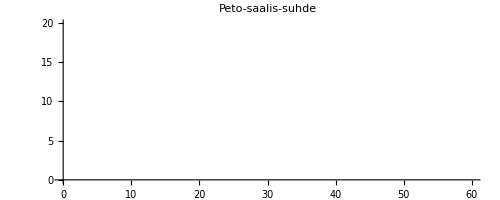

```mathematica
ClearAll["Global`*"]
a = 2;
b=0.2;
p=3;
q=0.1;
x0 = 30;
y0 = 10;

s=NDSolve[{x'[t] == a*x[t] - b*x[t]*y[t], y'[t] == -p*y[t] + q*x[t]*y[t], x[0] ==x0, y[0] == y0}, {x[t], y[t]}, {t,0,100}]
ParametricPlot[{x[t],y[t]}/.s, {t,0,20}, PlotLabel->"Peto-saalis-suhde"]
```

```mathematica
Solve[{a*x1-b*x1*y1==0,-p*y1+q*x1*y1==0}, {x1,y1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→0.,y1→0.},{x1→30.,y1→10.}}